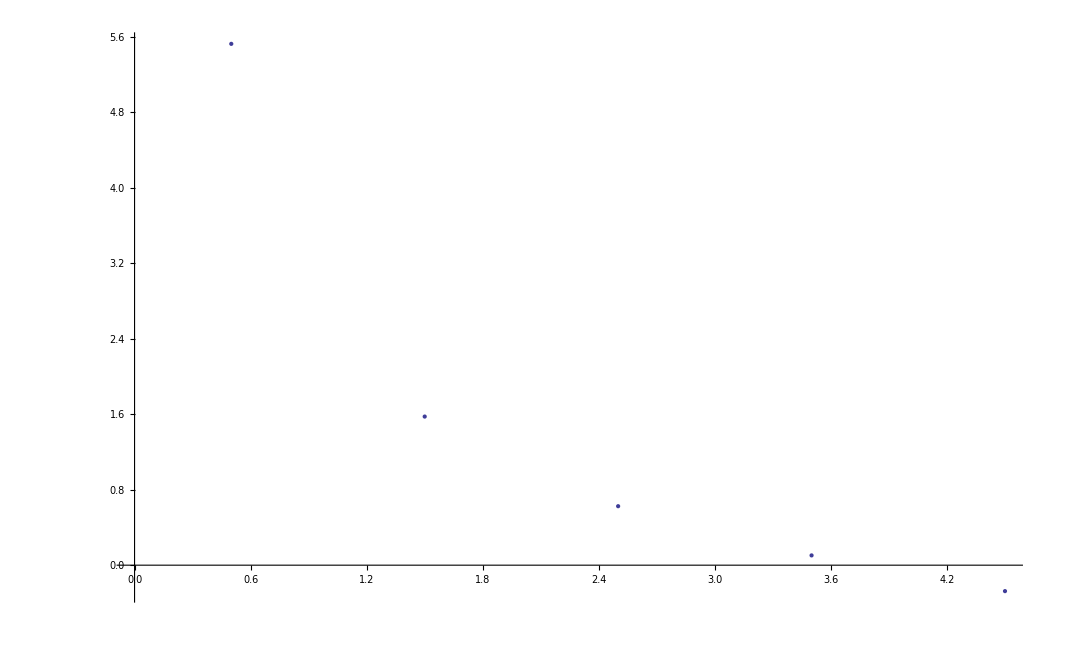

```mathematica
points = {.5,1.5,2.5,3.5,4.5};
w=1.5;l=.4;
length[n_]:=(w^2-n^2*l^2)/(2*n*l) ;
ListPlot[Transpose[{points,length[points]}]]
```